```mathematica
(*Likelihood*)
```

```mathematica
L=NormalDistribution[m1,0.15];
lik[x_,m_]:=PDF[L,x]/.m1->m;
```

```mathematica
lik[10,m]
```

2.65962 ⅇ^(-22.2222 (10-m)^2)

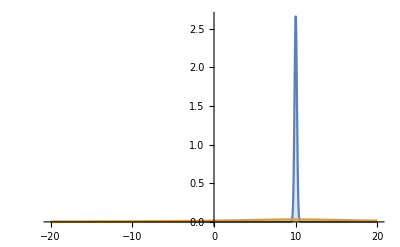

```mathematica
Data=10;
muhyp=10;
sighyp=10;
Plot[{lik[Data,μ],PDF[CauchyDistribution[muhyp,sighyp],μ]},{μ,-20,20},Filling->Axis, PlotRange->All]
```

```mathematica
lik[Data,μ]PDF[CauchyDistribution[muhyp,sighyp],μ]
```

(0.0846582 ⅇ^(-22.2222 (10-μ)^2))/(1+1/100 (-10+μ)^2)

```mathematica
Z=NIntegrate[lik[Data,μ]PDF[CauchyDistribution[muhyp,sighyp],μ], {μ,-Infinity, Infinity}]
```

0.0318238

```mathematica
Log[Z]
```

-3.44754

```mathematica
post[mu_]:=(lik[Data,mu]PDF[CauchyDistribution[muhyp,sighyp],mu])/Z
```

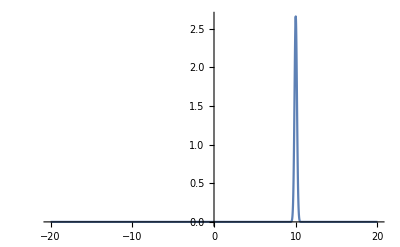

```mathematica
Plot[post[μ],{μ,-20,20},PlotRange->All]
```

```mathematica
NIntegrate[post[μ], {μ,-Infinity, Infinity}]
```

1.